```mathematica
data1 = Import["/net/home/f09/bajennissen/research/DAY190/tau_day_data/368nm.dat"];
data1hour=Drop[data1, None,1];
data2 = Import["/net/home/f09/bajennissen/research/DAY190/tau_day_data/412nm.dat"];
data2hour=Drop[data2,None,1];
data3 = Import["/net/home/f09/bajennissen/research/DAY190/tau_day_data/500nm.dat"];
data3hour=Drop[data3,None,1];
data4 = Import["/net/home/f09/bajennissen/research/DAY190/tau_day_data/610nm.dat"];
data4hour=Drop[data4,None,1];
data5 = Import["/net/home/f09/bajennissen/research/DAY190/tau_day_data/675nm.dat"];
data5hour=Drop[data5,None,1];
data6= Import["/net/home/f09/bajennissen/research/DAY190/tau_day_data/778nm.dat"];
data6hour=Drop[data6,None,1];
data7 = Import["/net/home/f09/bajennissen/research/DAY190/tau_day_data/862nm.dat"];
data7hour=Drop[data7,None,1];
```

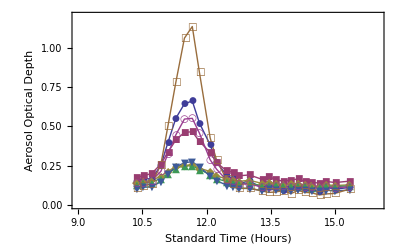

```mathematica
<<PlotLegends`
DataPlot=ListPlot[{data1hour,data2hour,data3hour,data4hour,data5hour,data6hour,data7hour}, PlotStyle->PointSize[0.02],PlotMarkers->Automatic,Joined->True,PlotLegend->{"368nm","412nm","500nm","610nm","675nm","778nm","862nm"},LegendPosition->{.22,.05}, LegendSize->{0.5,0.4},PlotRange->{{9,16},{0,1.2}},Frame->True, AxesOrigin-> {7,0},LegendShadow->None,FrameLabel->{{"Aerosol Optical Depth",""},{"Standard Time (Hours)","Day 190 July 9th, 2010"}}]
```